```mathematica
list = Import[NotebookDirectory[]<>"/res/out_0.0.txt","Table"];
Length[list]
len=Length[list[[1]]]
```

9

100

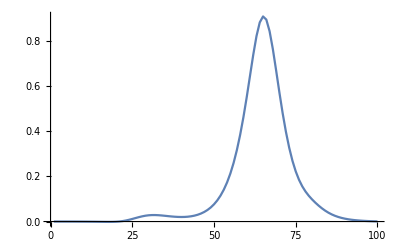

```mathematica
ListLinePlot[-list[[6]],PlotRange->All]
```

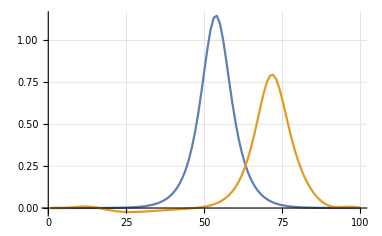

```mathematica
c=-list[[1]][[1]];
ListLinePlot[{-list[[1]]-c,-list[[-1]]-c},PlotRange->Full,GridLines->Automatic]
```

```mathematica
f1=NIntegrate[Interpolation[list[[1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[list[[-1]]^2,InterpolationOrder->2][x],{x,1,len-1}]
(f2-f1)/f1
```

27.1576

27.1581

0.0000190716